```mathematica
Off[General::"spell1"]
Off[General::"spell"]
SetDirectory["C:\\Users\\Matías\\Documents\\GitHub\\Tesis\\20180821\\Mediciones"];


			(*CARGA LA MATRIZ Y DETERMINA EL PERÍODO DE LA SEÑAL*)

Vext=-9000.0;fdbd=1/50.0; fstr=1/50.0;
mat=Import["Bobina 9.csv"];
lm=Length[mat];
V={};Idbd={};Istr={};
Do[AppendTo[V,{mat[[i,4]],mat[[i,5]]}];
AppendTo[Istr,{mat[[i,10]],fdbd*mat[[i,11]]}];AppendTo[Idbd,{mat[[i,16]],fstr*mat[[i,17]]}],{i,1,lm}];
indmax=Floor[N[Mean[Position[V[[All,2]],Max[V[[All,2]]]][[1]]]]];
indmin=Floor[N[Mean[Position[V[[All,2]],Min[V[[All,2]]]]]][[1]]];
tper=Abs[2*(V[[indmax,1]]-V[[indmin,1]])];
iper=Abs[2(indmax-indmin)];

indmaxstr=Floor[N[Mean[Position[V[[All,2]],Max[V[[All,2]]]][[1]]]]];
indminstr=Floor[N[Mean[Position[Istr[[All,2]],Min[Istr[[All,2]]]]]][[1]]];
tperstr=Abs[2*(Istr[[indmaxstr,1]]-Istr[[indminstr,1]])];

(*indmax=indice para el maximo de tension ; iper=cantidad de elementos en el periodo*)
```

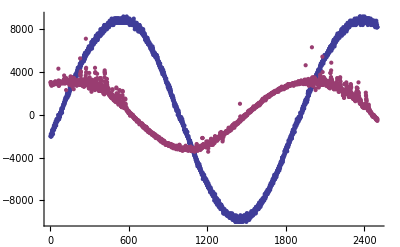

```mathematica
(*GRAFICA LAS SEÑALES*)
Istrcol=Istr[[All,2]];
Vcol=V[[All,2]];



voltaje=ListPlot[{Vcol,10^6*Istrcol}]
(*streamer=ListPlot[Istr]
Show[voltaje,streamer]*)
```

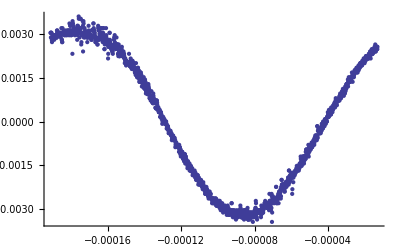

0.00040417

```mathematica
(*REOCRTE DE LOS PICOS DE LA SEÑAL CAPACITIVA APLICANDO TOLERANCIA AL FITEO EN ISTR*)
Istrrec=Istr;
niter=30;(*Número de veces que se desea iterar el recorte.*)
Do[
Faux=b*Cos[2*Pi/tper*t+c]+d;
Istrfit=Faux/.FindFit[Istrrec,Faux,{b,c,d},t];
Istrrec={};
datoscorte={};

Do[AppendTo[datoscorte,Istr[[indmax+i,2]]-Istrfit/.t->N[Istr[[indmax+i,1]]]],{i,-15,15}];
Corte=Mean[datoscorte];(*Establece una altura de pico para declarar la tolerancia al corte.Para ello,toma un promedio de 30 picos alrededor del pico mayor.*)
(*Corte=(Istr[[indmax,2]]-Istrfit/.t->N[Istr[[indmax,1]]])/2*)

Do[If[Istr[[i,2]]-(Istrfit/.t->N[Istr[[i,1]]])<Corte,AppendTo[Istrrec,{Istr[[i,1]],Istr[[i,2]]}],AppendTo[Istrrec,{Istr[[i,1]],Istrfit/.t->N[Istr[[i,1]]]}]],{i,1,iper}],{iter,1,niter}]

ListPlot[Istrrec, PlotRange->All]
Corte
```

P media streamers en W: 0.887083

Corriente media de streamers  en mA : 0.0785169

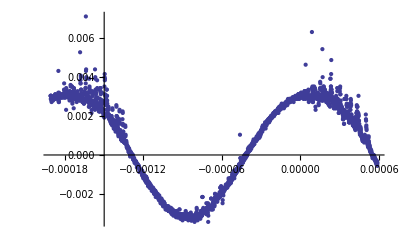

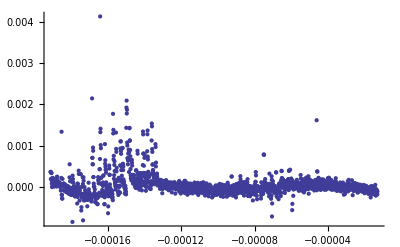

```mathematica
(* CÁLCULO DE POTENCIA Y CORRIENTE MEDIAS DE STREAMERS CON DESCUENTO DE SEÑAL       CAPACITIVA CON TOLERANCIA AL FITEO*)
avgpot={};Istrall={};Istravg={};


Faux=b*Cos[2*Pi/tper*t+c]+d;

Istrfit=Faux/.FindFit[Istrrec,Faux,{b,c,d},t];

Istraux={};

Do[AppendTo[Istraux,{Istr[[i,1]],Istr[[i,2]]-Istrfit /. t->Istr[[i,1]]}],{i,1,iper}];

Vmax=Max[V[[All,2]]];
Vmin=Min[V[[All,2]]];
Vacm=0.5(Vmax+Vmin);
Vdc=Vacm-Vext;
pot=0.0;Istravg=0.0;
Do[pot+=Istraux[[i,2]]*(V[[i,2]]-Vacm+Vdc);Istravg+=Istr[[i,2]],{i,1,iper}];
avgpot=pot/iper;
Istravg=Istravg/iper;
StringJoin["P media streamers en W: ",ToString[avgpot]]
StringJoin["Corriente media de streamers  en mA : ",ToString[10^3*Istravg]]

Pf2=Plot[Istrfit,{t,V[[1,1]],V[[iper,1]]},PlotRange->All];
Poriginal=ListPlot[Istr,PlotRange->All];
Show[Pf2,Poriginal]
ListPlot[Istraux,PlotRange->All]
```

```mathematica
(*REOCRTE DE LOS PICOS DE LA SEÑAL CAPACITIVA APLICANDO TOLERANCIA AL FITEO EN IDBD*)

Idbdrec=Idbd;
niter=20; (*Número de veces que se desea iterar el recorte.*)
Do[
Faux=b*Cos[2*Pi/iper*t+c]+d;

Idbdfit=Faux/.FindFit[Idbdrec,Faux,{b,c,d},t];

Idbdrec={};
datoscorte={};
Do[AppendTo[datoscorte,Idbd[[indmax+i,2]]-Idbdfit /. t->N[Istr[[indmax+i,1]]]],{i,-15,15}];
Corte=Mean[datoscorte]; (*Establece una altura de pico para declarar la tolerancia al corte. Para ello, toma un promedio de 30 picos alrededor del pico mayor.*)
 

Do[If[Abs[Idbd[[i,2]]- (Idbdfit /. t->N[Idbd[[i,1]]])]<Corte,AppendTo[Idbdrec,{Idbd[[i,1]],Idbd[[i,2]]}],AppendTo[Idbdrec,{Idbd[[i,1]],Idbdfit /. t->N[Idbd[[i,1]]]}]],{i,1,iper}],{iter,1,niter}]

Pdbd=ListPlot[Idbd, PlotRange->All];
Pfitdbd=ListPlot[Idbdfit, PlotRange-> All];
Show[Pdbd,Pfitdbd]
ListPlot[Idbdrec, PlotRange->All]
```

```mathematica
ListPlot[Idbdrec]
```

```mathematica
(* Cálculo de potencia y corriente medias de dbd *)
avgpot={};Idbdall={};Idbdavg={};
ninter=300;


(*lm0=Floor[iper/ninter];minis={};maxis={};
Do[aux=Max[Idbd[[(i-1)lm0+1;;i*lm0,2]]];If[aux>0,AppendTo[minis,aux]];aux=Min[Idbd[[(i-1)lm0+1;;i*lm0,2]]];If[aux<0,AppendTo[maxis,aux]],{i,1,ninter}];
Iplus=Mean[minis];Imin=Mean[maxis];
Idbdaux={};
Do[If[Idbd[[i,2]]>Iplus,AppendTo[Idbdaux,{Idbd[[i,1]],Idbd[[i,2]]-Iplus}],If[Idbd[[i,2]]<Imin,AppendTo[Idbdaux,{Idbd[[i,1]],Idbd[[i,2]]-Imin}],AppendTo[Idbdaux,{Idbd[[i,1]],0}]]],
{i,1,iper}];*)


Vmax=Max[V[[All,2]]];
Vmin=Min[V[[All,2]]];
Vacm=0.5(Vmax+Vmin);
Vdc=Vacm-Vext;
pot=0.0;Idbdavg=0.0;
Do[pot+=Idbdaux[[i,2]]*(V[[i,2]]-Vacm);Idbdavg+=Idbd[[i,2]],{i,1,iper}];
avgpot=pot/iper;
Idbdavg=Idbdavg/iper;
StringJoin["P media de DBD en W: ",ToString[avgpot]]
StringJoin["Corriente media de DBD  en mA : ",ToString[10^3*Idbdavg]]
```

P media de DBD en W: 5.37364

Corriente media de DBD  en mA : 20.5933

```mathematica
ListPlot[Idbdaux,PlotRange->All]
```

```mathematica
ListPlot[Istr,PlotRange->All]
```

```mathematica
ListPlot[Idbd,PlotRange->All]
```